```mathematica
Clear["Global`*"];
```

# Aβ40

#### Normalised data (from amylofit)

```mathematica
SetDirectory[NotebookDirectory[]]
data0=Import["Input_files/AB40/0D/data.tsv"];
data0=Delete[data0,1];
data2=Import["Input_files/AB40/2D/data.tsv"];
data2=Delete[data2,1];
data5=Import["Input_files/AB40/5D/data.tsv"];
data5=Delete[data5,1];
data10=Import["Input_files/AB40/10D/data.tsv"];
data10=Delete[data10,1];
```

/Users/gabiheller/Desktop/Heller_10074_G5_data_code/ThT_aggregation/Kinetic modelling

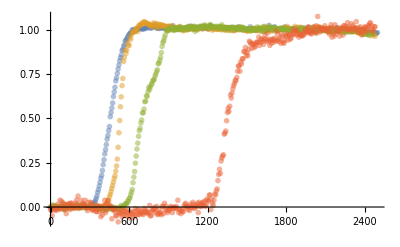

```mathematica
dataplot=ListPlot[{data0,data2,data5,data10},PlotMarkers->{•,6},PlotStyle->Opacity[0.5]]
```

#### Unnormalised data

```mathematica
rawdata0=Import["Input_files/AB40/Raw_data_0D_2D_5D_10D/data.tsv",{"Data",All,{1,2}}];
rawdata0=Delete[rawdata0,1];
rawdata2=Import["Input_files/AB40/Raw_data_0D_2D_5D_10D/data.tsv",{"Data",All,{3,4}}];
rawdata2=Delete[rawdata2,1];
rawdata5=Import["Input_files/AB40/Raw_data_0D_2D_5D_10D/data.tsv",{"Data",All,{5,6}}];
rawdata5=Delete[rawdata5,1];
rawdata10=Import["Input_files/AB40/Raw_data_0D_2D_5D_10D/data.tsv",{"Data",All,{7,8}}];
rawdata10=Delete[rawdata10,1];
```

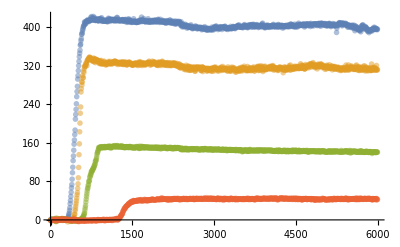

```mathematica
rawdataplot=ListPlot[{rawdata0,rawdata2,rawdata5,rawdata10},PlotMarkers->{•,6},PlotStyle->Opacity[0.5]]
```

#### Normalization factors (from amylofit):

```mathematica
rawdata2[[250]][[1]]
```

1494.

```mathematica
lmax=340;
```

data 0: normalization on last 140 points in plateau

```mathematica
l=100;
norm0=1/l*Sum[rawdata0[[n]][[2]],{n,lmax-l,lmax}]
```

416.549

data 2: normalization on 200 points in plateau

```mathematica
l=100;
norm2=1/l*Sum[rawdata2[[n]][[2]],{n,lmax-l,lmax}]
```

327.516

data 5: normalization on 200 points in plateau

```mathematica
l=100;
norm5=1/l*Sum[rawdata5[[n]][[2]],{n,lmax-l,lmax}]
```

151.723

data 10: normalization on 100 points in plateau

```mathematica
l=50;
norm10=1/l*Sum[rawdata10[[n]][[2]],{n,lmax-l,lmax}]
```

42.663

## Global fit

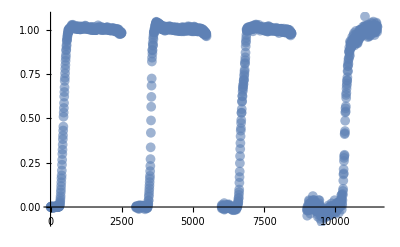

```mathematica
data={};
For[i=0,i<Length[data0],i++,
data=Append[data,{data0[[i+1,1]],data0[[i+1,2]]}]
]

For[i=0,i<Length[data2],i++,
data=Append[data,{data2[[i+1,1]]+3000,data2[[i+1,2]]}]
]

For[i=0,i<Length[data5],i++,
data=Append[data,{data5[[i+1,1]]+6000,data5[[i+1,2]]}]
]

For[i=0,i<Length[data10],i++,
data=Append[data,{data10[[i+1,1]]+9000,data10[[i+1,2]]}]
]

dataplottot=ListPlot[{data},PlotMarkers->{Automatic,10},PlotStyle->Opacity[0.6]]
```

#### Perform the global fit

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-2488.89] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
Keq | 0.098846 | 0.000555292 | 178.007 | 0.

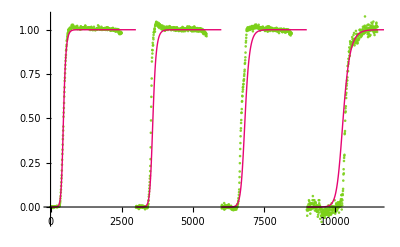

```mathematica
Clear[Keq]
mtot=10.*10^(-6);
kp=3*10^6*60;
kn=20.2/kp;
k2=4.26*10^(11)/kp;
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];
theta=2/(2*3);

i01=2.;
i02=5.;
i03=10.;

(*Mass formula*)

Mass[t_,lambda_,kappa_]:=1-(((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]+Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t]))*((((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2)Exp[kappa*t])/(((kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]-Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2])/(2kappa))+lambda^2/(2kappa^2))))^(kappa*(theta+(2/nc)*lambda^2/kappa^2)/(Sqrt[kappa^2*(theta+(2/nc)*lambda^2/kappa^2)+lambda^4/kappa^2]))*Exp[-kappa*Sqrt[theta+(2/nc)*lambda^2/kappa^2]*t];

(* Fitting function *)

nlm=NonlinearModelFit[data,Piecewise[{{Mass[t,λ,κ],t<3000},{Mass[t-3000,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],3000≤t<6000},{Mass[t-6000,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],6000≤t<9000},{Mass[t-9000,λ*(1/(1+Abs[Keq]*i03))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i03))^((n2+1)/2)],9000≤t<12000}}],{{Keq,0.1}},t];
(*Print fitting parameters*)
nlm["ParameterTable"]

Show[
ListPlot[{data},PlotStyle->{{RGBColor[.482,.816,.098],Opacity[0.9]}}],Plot[{nlm[t]},{t,0,12000},PlotStyle->{{RGBColor[.9,.02,.45],Thick}},PlotRange->All]]
```

```mathematica
1/0.09884598460316313
```

10.1167

#### Plot global fit

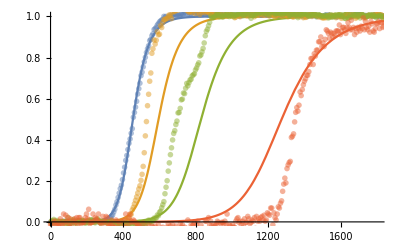

```mathematica
mtot=10.*10^(-6);
kp=3*10^6*60;
kn=20.2/kp;
k2=4.26*10^(11)/kp;
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

Keq=0.09884598460316313; (*FROM GLOBAL FIT*)

i01=2.;
i02=5.;
i03=10.;

(*Plot solutions*)
Show[Plot[{Mass[t,λ,κ],Mass[t,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],Mass[t,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],Mass[t,λ*(1/(1+Abs[Keq]*i03))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i03))^((n2+1)/2)]},{t,0,2000},PlotRange->{{0,1800},{0,1}}],dataplot]
```

#### Export data as xls

```mathematica
m0=Table[{t,Mass[t,λ,κ],Mass[t,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],Mass[t,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],Mass[t,λ*(1/(1+Abs[Keq]*i03))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i03))^((n2+1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["Fit2.xls",m0,"XLS"]
```

Fit2.xls

#### Plot global fit on raw data

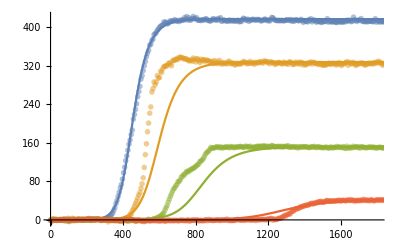

```mathematica
mtot=10.*10^(-6);
kp=3*10^6*60;
kn=20.2/kp;
k2=4.26*10^(11)/kp;
nc=2;
n2=2;
λ=Sqrt[2*kp*kn*mtot^2];
κ=Sqrt[2*kp*k2*mtot^3];

Keq=0.1015203058194996; (*FROM GLOBAL FIT*)

i01=2.;
i02=5.;
i03=10.;

(*Plot solutions*)
Show[Plot[{norm0*Mass[t,λ,κ],
norm2*Mass[t,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],norm5*Mass[t,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],norm10*Mass[t,λ*(1/(1+Abs[Keq]*i03))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i03))^((n2+1)/2)]},{t,0,2000},PlotRange->{{0,1800},All}],rawdataplot]
```

#### Export data as xls

```mathematica
m0=Table[{t,norm0*Mass[t,λ,κ],
norm2*Mass[t,λ*(1/(1+Abs[Keq]*i01))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i01))^((n2+1)/2)],norm5*Mass[t,λ*(1/(1+Abs[Keq]*i02))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i02))^((n2+1)/2)],norm10*Mass[t,λ*(1/(1+Abs[Keq]*i03))^((nc+1)/2),κ*(1/(1+Abs[Keq]*i03))^((n2+1)/2)]},{t,0,3000,1}];
m0//TableForm;

Export["Fit_Ab40_raw.xls",m0,"XLS"]
```

Fit_Ab40_raw.xls